# The Other Completion ℚ_p: P-adic Expansions, Hensel’s Lemma, and Non-Archimedean Calculus

```mathematica
PacletDirectoryLoad["/Users/frank/Documents/Wolfram"];
PacletInstall["PadicNumbers"];
Needs["PadicNumbers`"]
```

## Down the rabbit hole

## Something is wrong with these numbers

Run this and stare at it for a moment:

```mathematica
Table[Mod[-1,3^k],{k,1,10}]
```

{2,8,26,80,242,728,2186,6560,19682,59048}

These numbers are racing toward infinity. And yet, in a precise mathematical sense, they are converging — to negative one.
Check: every one of them, plus 1, is divisible by the highest power of 3 available:

```mathematica
Table[{k,Mod[-1,3^k],Mod[Mod[-1,3^k]+1,3^k]},{k,1,8}]//TableForm
```

1 | 2 | 0
2 | 8 | 0
3 | 26 | 0
4 | 80 | 0
5 | 242 | 0
6 | 728 | 0
7 | 2186 | 0
8 | 6560 | 0

Now look at what these numbers are in base 3:

```mathematica
Table[BaseForm[Mod[-1,3^k],3],{k,1,8}]//TableForm
```

2_3
22_3
222_3
2222_3
22222_3
222222_3
2222222_3
22222222_3

Each step just prepends another 2 on the left. The “limit” is the infinite string ...2222222 — all 2’s extending forever leftward. 

This is -1.

If that feels like a trick, here is another one. We all know √2 is irrational — it cannot be written as a fraction, and it certainly is not an integer. But:

```mathematica
Table[{k,Mod[-2,7^k],Mod[Mod[-2,7^k]^2,7^k]},{k,1,7}]//TableForm
```

1 | 5 | 4
2 | 47 | 4
3 | 341 | 4
4 | 2399 | 4
5 | 16805 | 4
6 | 117647 | 4
7 | 823541 | 4

The middle column is 5, 47, 341, 2399, ... — again exploding. But every single one of them, when squared, gives 2 (mod 7^k). These are successive approximations to √2. Not in the reals, where √2 lives between 1 and 2. In some other number system, where √2 looks like an integer with infinitely many digits extending to the left.

Two questions should now be nagging:

   1. In what sense are diverging integers “converging”?
   2. Is this a curiosity, or is there real mathematics here?

The answer to the first question leads to p-adic numbers. The answer to the second is that these numbers underpin some of the deepest results in modern number theory — including the proof of Fermat’s Last Theorem.

## Two Ways to Measure Distance

In the reals, two numbers are close when their difference is small: |47 - 5| = 42, which is not small, so 47 and 5 are far apart. End of story.

But there is another ruler. Instead of asking “how big is the difference?”, ask “how many times does 7 divide the difference?”:

```mathematica
diffs=Table[Module[{a=Mod[-2,7^k],b=Mod[-2,7^(k+1)]},{k,a,b,b-a,IntegerExponent[b-a,7],N[7^-IntegerExponent[b-a,7]]}],{k,1,6}];
Grid[Prepend[diffs,{"k","a(k)","a(k+1)","Δ",Subscript["v",7],Subscript["|·|",7]}],Frame->All,Alignment->Center,Background->{None,{Blue,None}}]
```

k | a(k) | a(k+1) | Δ | v_7 | (|·|)_7
1 | 5 | 47 | 42 | 1 | 0.142857
2 | 47 | 341 | 294 | 2 | 0.0204082
3 | 341 | 2399 | 2058 | 3 | 0.00291545
4 | 2399 | 16805 | 14406 | 4 | 0.000416493
5 | 16805 | 117647 | 100842 | 5 | 0.000059499
6 | 117647 | 823541 | 705894 | 6 | 8.49986×10^-6

The 7-adic absolute value of each successive difference is (|·|)_7=7^(-k) , which is collapsing to zero. In this metric, 5, 47, 341, 2399, ... is a Cauchy sequence. It converges — just not in ℝ.

The rule is simple: two integers are p-adically close when their difference is divisible by a high power of p. The low digits (ones, p’s, p’s squared) are the important ones. The coefficient of p^100 is a tiny perturbation. This is the exact reverse of how we usually think about size.

### Expanding right, expanding left

In decimal, we approximate by expanding to the right:

    16/7 ≈ 2.2 → 2.28 → 2.285 → 2.2857 → ...

Each new digit is a smaller correction — a fraction of a power of 10. We are summing negative powers of the base, and convergence means these corrections shrink to zero in the usual absolute value.

The examples above do the opposite: they expand to the left, adding higher positive powers of p. In the 3-adic world, -1 is the series

    2 + 2·3 + 2·3^2 + 2·3^3 + ...

This diverges in ℝ. But each partial sum is congruent to -1 modulo a higher power of 3, so the partial sums converge 3-adically. The same series, two different verdicts, depending on which ruler you use.

The digit tree makes this concrete. Each infinite path from root to boundary is a leftward digit expansion. The number -1 is the path that always chooses branch 2. The number -2 always chooses branch 1:

```mathematica
Table[{k,BaseForm[Mod[-2,3^k],3]},{k,1,8}]//TableForm
```

1 | 1_3
2 | 21_3
3 | 221_3
4 | 2221_3
5 | 22221_3
6 | 222221_3
7 | 2222221_3
8 | 22222221_3

...111111 in base 3. Every negative integer corresponds to an eventually periodic path. Every positive integer is a finite path (it terminates in 0’s). The p-adic integers contain all of ℤ — positive and negative — as infinite digit strings growing leftward.

### There is no third option (Ostrowski’s theorem)

We have seen two ways to measure distance on the rationals: the usual absolute value and the p-adic one. Are there others?

Ostrowski’s theorem says no. Every nontrivial absolute value on ℚ is equivalent to exactly one of:
    • The usual absolute value |·| → completing ℚ gives ℝ
    • The p-adic absolute value (|·|)_7, one for each prime p → completing gives ℚ_p 

The rationals sit inside both worlds simultaneously. Every question about ℚ can be studied from the real side, from the p-adic side for each prime, or — most powerfully — from all sides at once. This is the local-global philosophy that drives modern number theory: a problem over ℚ is equivalent to a family of problems, one over ℝ and one over each ℚ_p.

### Two completions, two worlds

Completing ℚ with the usual absolute value gives ℝ — a connected continuum supporting classical calculus. Limits, derivatives, integrals: all built on the fact that nearby points can be connected by a continuous path.

Completing with the p-adic absolute value gives ℚ_p — a totally disconnected field. There are no arcs, no smooth paths between points. Every open ball is simultaneously closed, so the space shatters into clopen pieces at every scale. The topology is not a continuum but a fractal dust, homeomorphic to the Cantor set.

This means there is no continuum-dependent calculus: no usual derivative, no Riemann integral. And yet, as we will see, a rich form of harmonic analysis survives — not because of smoothness, but because the group structure and measure theory are enough.

## The hyperbolic tree and the circle illusion

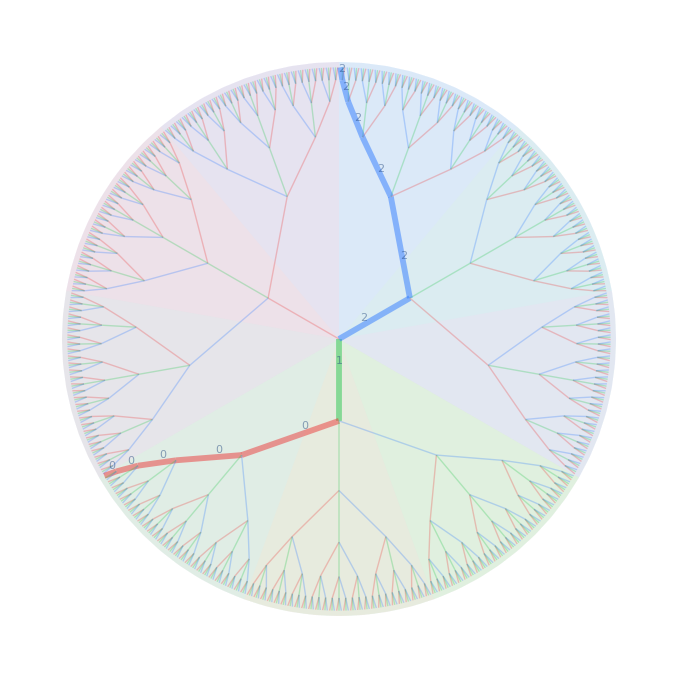

```mathematica
PadicDigitTree[3,6,RayDigits->{Padic[-1,3],Padic[1,3]},EdgeLabelMode->"Ray",SectorBackground->True,SectorBackgroundDepth->2,Background->None]
```

This image shows the 3-adic integers embedded as a rooted tree in the Poincaré disk. Each path from the center outward represents successive digits in a 3-adic expansion — at every node, the tree branches into three children (colored red, green, blue for digits 0, 1, 2). The highlighted path, for instance, traces the digit sequence 2 → 0 → 1, meaning deeper levels of p-adic precision.

Because the layout fans these branches radially toward a circular boundary, it is tempting to conclude that the p-adic integers ℤ_p or the set of ℚ_p are topologically a circle S.b9. This is false. The boundary of the disk is merely a convenient canvas — the actual space of infinite digit sequences {0, 1, 2}^ℕ carries the product topology, which is totally disconnected, compact, and perfect. That makes ℤ_p homeomorphic to the Cantor set, not to S.b9.

The decisive invariant is connectedness: S.b9 is connected (you cannot split it into two disjoint open sets), while ℤ_p is the opposite — every open ball is simultaneously closed, so the space shatters into clopen pieces at every scale. In the p-adic metric, two numbers are “close” when they share a long initial prefix of digits, producing a tree-like ultrametric rather than the arc-length metric of a circle. The dust of endpoints you see crowding the rim is genuinely dust — a Cantor-like fractal, not a continuous curve. This is visible in the sector coloring: moving along the boundary of the disk, the background color never transitions smoothly — it jumps abruptly at every sector boundary, and within each sector, it jumps again at every sub-sector. This self-similar discontinuity at every scale is the visual signature of total disconnectedness.

As the caption reminds us, completing ℚ with the usual absolute value gives ℝ (a connected continuum supporting classical calculus), whereas completing with each p-adic absolute value |·|_p gives ℚ_p — a totally disconnected field where the familiar derivative and integral of real analysis have no direct analogue. The geometry encoded in this tree is hierarchical and discrete at every resolution, which is precisely what makes p-adic analysis so different from the real case.

The self-similar branching visible in this papyrus capital from Edfu reminds us that hierarchical subdivision has been an architectural and decorative motif for millennia — long before the formal mathematics of fractal geometry or p-adic analysis gave it a name. Whether this reflects deep geometric intuition or simply the structure of papyrus itself is an open question worth pondering.
-Graphics-

#### Why does this matter at all?

Number theory. The Hasse–Minkowski theorem says a quadratic form has rational solutions if and only if it has solutions in ℝ and in ℚ_p for every prime p. The p-adics turn global arithmetic questions into local ones.

Physics. p-adic string theory and p-adic quantum mechanics explore ultrametric spaces as alternatives to the real continuum at Planck-scale distances, where the triangle inequality becomes the stronger ultrametric inequality: |x + y|_p≤ max(|x|_p,| y|_p) .

Computation. Hensel’s lemma — the p-adic analogue of Newton’s method — lifts solutions modulo p to solutions modulo p.b2, p.b3, etc. This is the backbone of algorithms in computer algebra.

Analysis. The p-adics are totally disconnected and yet locally compact — a topological structure radically different from ℝ. Doing calculus here forces you to rethink what continuity, integration, and differentiation really mean.

## Analysis in ultrametric ℚ_p space, discreet Fourier transform

The Fourier transform on ℚ_p exists not because of any notion of “smoothness” or “continuous oscillation,” but because the group structure and measure theory are sufficient. The “frequencies” aren’t sine waves — they’re characters that are locally constant and take only finitely many values on compact subsets. It’s harmonic analysis without harmonics in the classical sense.

#### What Dies

On ℝ, calculus rests on three pillars: Limits → survive formally (ℚₚ is a complete metric space), but behave very differently. Sequences converge iff their terms go to zero in |·|ₚ, which means the digits stabilize from the left. This is fine algebraically but geometrically it’s convergence “down the tree,” not along a line.

Derivatives → the formal definition f’(a) = lim(f(a+h)−f(a))/h exists for certain functions, but it’s almost useless. The problem: on a totally disconnected space, knowing f in a neighborhood of a tells you f on a clopen ball, but the function can do completely unrelated things on a neighboring ball at the same scale. The derivative doesn’t constrain global behavior. There are no differential equations worth writing down, because a local derivative can’t “propagate” information across a disconnected space.

The intermediate value theorem → completely fails. Continuous functions on ℚₚ can jump between values without passing through intermediates, because there’s no connected path forcing them through.

So the entire edifice of classical analysis — ODEs, Taylor series as local-to-global tools, the idea that knowing a function “nearby” constrains it “far away” — collapses.

#### What Survives

Three things survive, and they’re enough:
1. Haar Measure (Integration)
ℚₚ is a locally compact abelian group, so it has a unique (up to normalization) translation-invariant measure. Integration works fine:
∫Qpf(x) dx\int_{\mathbb{Q}_p} f(x) \, dx∫Qp​​f(x)dx

is well-defined for integrable functions. The measure of a ball of radius pⁿ is just pⁿ. This is the one piece of “calculus” that transfers directly — you can integrate, compute volumes, define L.b2 spaces. The reason it survives is that it’s algebraic (group structure), not topological (connectedness).

## Implementing an exact ℚ representation in ℚ_p

## The Basics

### Everything follows from the PadicOrder (Valuation)

Everything in p-adic arithmetic rests on one question: given a rational number and a prime p, how many times does p divide it? 
This count is called the p-adic order (or valuation), written ν_p. From it, everything else follows. The p-adic absolute value is p raised to the negative order:

75 = 3 × 5^2, so ν_5(75)=2. The number 7 has no factors of 5, so ν_5(7)=20. And 3/25=3×5^-2, so its order is -2. The pattern: positive order means p divides the number, negative means p is in the denominator, zero means p is absent entirely.

```mathematica
{PadicOrder[75,5],PadicOrder[7,5],PadicOrder[3/25,5]}
```

{2,0,-2}

v_p(n)=Piecewise[{{max{k∈ℕ:p^k|n}, n!=0}, {∞, n=0}}]
with
v_p(n)<=log_p n, v_p(n/d)=v_p(n)-v_p(d)
also with the following properties
ν_p(x ·y)=ν_p(x )+ν_p(y) and ν_p(x +y)>=min{ν_p(x ),ν_p(y)} with strict equality iff x!=y

0<=(|x|)_p=p^(-ν_p(x ))<∞ and 0=(|x|)_p iff x = 0
hence the following properties hold
(|x ·y|)_p=(|x |)_p(|y|)_p
(|x +y|)_p<=max{(|x |)_p,(|y|)_p}
and with it the non-archimedian shift invariant distance
dist(x,y)=(|x -y|)_p
and the triangle inequality
dist(x,z)<=dist(x,y)+dist(y,z)

### A faithful representation of ℚ⊂ℚ_p

Given any prime number p, then with Bézout’s identity or what Mathematica calls extended GCD, x d+y p=1 for co-prime gcd(d, p) = 1, there is a unique series expansion in powers of p to positive (infinite) orders. This construction is based on writing a rational number with co-prime numerator n and denominator d as

r=p^k n/d=p^k n/d(t d+u p)=a p^k+p^(k+1)(q d+u n)/d=a p^k+p^(k+1)n'/d

and 0<=a<p. Further a,q,u are uniquely determined! As an example, to determine the unique factor we can use the following for the example with r=1/3 and p=5

```mathematica
ExpandToPowerOf[p_Integer/;p>1]:=Function[{r},({#[[2]]r,0}+QuotientRemainder[#[[1]] Numerator[r],p])&[ExtendedGCD[Denominator[r], p][[2]]]]
```

Mathematica implements rational numbers in such a way that numerator and denominator are made co-prime, hence they don’t have any common factors.  Further, in order to ensure co-primality with regards to the base p we simply use the PadicNormalize function:

```mathematica
ExpandToPowerOf[5][PadicNormalize[1/3,5]]
```

{-1/3,2}

Applying (1) iteratively leads to a potentially infinite but eventually periodic formal power series for a rational number in p-adic expansion, and to a finite expansion when the r is a positive integer (then this is just the regular base p expansion):

r=∑_(j=k)^∞ a_j p^j

```mathematica
Last/@Drop[NestList[ExpandToPowerOf[3][#[[1]]]&,{PadicNormalize[-20000/11,3],0},15],1]
```

{2,2,0,0,2,0,0,1,1,0,2,2,1,1,0}

For general rational numbers the coefficients a_j exhibit eventual periodicity, as shown in the example above. Hence, formally we can use the geometric series summation to represent it.  A rational number’s p-adic expansion is always eventually periodic.

(a_0 a_1 a_2… a_(k-1))_p=∑_(j=0)^(k-1) a_j p^j, r=(a_0 a_1 a_2… a_(k-1))_p(p^0+p^k+p^(2k)+…)=-(a_0 a_1 a_2… a_(k-1))_p 1/(p^k-1)

a rational number in the interval [-1,0) with a periodicity of length k>0. The difference between purely and eventually periodic is that in the later case we have a non-repeating beginning part

r=(a_0 a_1 a_2(…a)_(j-1))_p+p^j(a_j a_(j+1)a_(j+2)(…a)_(j+k-1))_p(p^0+p^k+p^(2k)+…)=(a_0 a_1 a_2(…a)_(j-1))_p-p^j(b_0 b_1 b_2(…b)_(k-1))_p 1/(p^k-1)

For a faithful representation of any rational number r∈ ℚ in its p-adic expansion ℚ_p we need to know three parts:

1.) The index of the first non-zero coefficient in the expansion (this can be a negative one), this is given by PadicOrder
2.) The non-repeating  part, we call this mantissa here.
3.) The length of the periodicity and the value of the periodic part.

```mathematica
Drop[NestList[ExpandToPowerOf[3][#[[1]]]&,{PadicNormalize[-20000/11,3],0},10],1]
```

{{-6674/11,2},{-2232/11,2},{-744/11,0},{-248/11,0},{-90/11,2},{-30/11,0},{-10/11,0},{-7/11,1},{-6/11,1},{-2/11,0}}

It’s easy to monitor a repeated state  to determine both, length of non-periodicity and periodicity:

```mathematica
PadicSignature[20000/11,3]
```

{12,5}

## Rational numbers with efficient ℚ_p representation

Let’s revisit the general representation of a p-adic rational number

r=(a_0 a_1 a_2(…a)_(j-1))_p+p^j(a_j a_(j+1)a_(j+2)(…a)_(j+k-1))_p(p^0+p^k+p^(2k)+…)=(a_0 a_1 a_2(…a)_(j-1))_p-p^j(b_0 b_1 b_2(…b)_(k-1))_p 1/(p^k-1)

Separating the non-periodic and periodic parts introduces code complexity. We reduce this by combining both into a single significand. PadicRational[m, p, e, N, k] is a p-adic floating-point format: m is the significand, e is the exponent (valuation), p is the base, N is the total precision (= non-period + period length), and k encodes the periodicity. The analogy to IEEE 754’s (sign, exponent, mantissa) is natural but richer because k captures the exact repeating structure that rationals have.

PadicRational[(a_0 a_1 a_2(…a)_(j-1))_p+p^j(b_0 b_1 b_2(…b)_(k-1))_p,p,e,N,k] // Normal -> Rational[n,d]  N=j+k
PadicRational[m,p,e,N,k] // Normal -> Mod[m,p^j] - p^j Quotient[m,p^j]/(p^k-1)  N=j+k
PadicRational[m,p,e,N,0] // Normal -> m * p^e

### Four Cases of Integer and Rational P-adic Expansions

#### Case 0: Non-negative integers ℤ_(>=0)

The p-adic expansion of a positive integer or 0 is just the regular finite base-p expansion:

r=(a_0 a_1 a_2(…a)_(k-1))_p=∑_(j=0)^(k-1) a_j p^j <p^k with k=⌈log_p[-r]⌉

#### Case 1: Negative integers (-r > 0)

Since, (-r) is positive and is smaller than some p^k we can find a p-adic expansion of  the positive integer R=p^k-(-r) as in the case above:

p^k-(-r)=R=Mod[r,p^k]=(c_0 c_1 c_2(…c)_(k-1))_p=∑_(j=0)^(k-1) c_j p^j

A direct consequence of the formal infinite power series expansion is that we have a simple representation for the negative integer -1 and for -p^k

-1=(p-1p-1…)_p=∑_(j=0)^∞ (p-1)p^j=(p-1)/(1-p)  and therefor-p^k=∑_(j=k)^∞ (p-1)p^j

therefore finally we have the infinite eventually periodic expansion of a negative integer

r=R-p^k=(p^k-(-r))-p^k=∑_(j=0)^(k-1) c_j p^j +∑_(j=k)^∞ (p-1)p^j=(c_0 c_1 c_2(…c)_(k-1))_p+p^k(p-1)_p/(1-p)

#### Negation process for integers and general rational numbers

Now, we can formalize this process in from of negation, consider the expansion of a positive integer (-r) and write it in 2 ways,

-r=(a_0 a_1 a_2(…a)_(k-1))_p and r=-(-r)=(c_0 c_1 c_2(…c)_(k-1))_p+p^k(p-1)_p/(1-p)

also we can write it another way

r=1+(-1)-(-r)=[1+(p-1)-a_0]p^0+∑_(j=1)^(k-1) (p-1-a_j)p^j+∑_(j=k)^∞ (p-1)p^j

Hence, we identity

c_0=p-a_0   and  c_j=(p-1)-a_j for j>=1 or equivalently
(c_0 c_1 c_2(…c)_(k-1))_p = 1+(p-1)(p^k-1)/(p-1)-(a_0 a_1 a_2(…a)_(k-1))_p=p^k-(a_0 a_1 a_2(…a)_(k-1))_p=Mod[-(a_0 a_1 a_2(…a)_(k-1))_p,p^k]

#### Case 2a, purely periodic expansion: r is a negative rational in [-1,0) with absolute value 1

Theorem 2.  A rational number with p-adic absolute value 1 has a purely periodic p-adic expansion if and only if it lies in the real interval [−1, 0).

We already cleared that any purely periodic p-adic expansion with valuation 1 represents a rational number in [-1,0)

(a_0 a_1 a_2(…a)_(k-1))_p=∑_(j=0)^(k-1) a_j p^j, r=(a_0 a_1 a_2(…a)_(k-1))_p(p^0+p^k+p^(2k)+…)=-(a_0 a_1 a_2(…a)_(k-1))_p 1/(p^k-1)

Conversely, we can show that any rational number in [-1,0) leads to such an expansion, here is how it goes: Assume that n, d and p are pairwise co-prime, with 0<n<=d, hence there is a lowest k for which p^k=1 mod d ⧦ p^k= 1 + d b

-1<=r=-n/d==-(n b)/(d b)=-(n b)/(p^k-1)=N/(1-p^k)=(a_0 a_1 a_2(…a)_(k-1))_p(p^0+p^k+p^(2k)+…)<0

We could do an exhaustive search for the exponent k (is there an upper limit on k?), an example for -5/11in 3-adic expansion
Also since -1<=N=n b < p^k-1 we just have a simple integer expansion in base-p at most of length k with N=(a_0 a_1 a_2(…a)_(k-1))_p

#### Case 2b, negating purely periodic expansion: r is a positive rational in (0,1) with absolute value 1

There are 2 ways to handle this case, we could write R=r-1 and R  is a rational for which case 2a applies

r=1+(r-1)=1+R=1+(c_0 c_1 c_2(…c)_(k-1))_p(p^0+p^k+p^(2k)+…)=(1+c_0)+p(c_1 c_2 c_3(…c)_(k-1)c_0)_p(p^0+p^k+p^(2k)+…)

This results in an eventually periodic expansion with the only a single digit as a non-repeating part. Further we can use the following relationships for its computation

(c_1 c_2 c_3(…c)_(k-1))_p,c_0=QuotientRemainder[(c_0 c_1 c_2(…c)_(k-1))_p,p]

Hence, we can implement a simple rotate left operation that leaves the length of the periodicity unchanged. RotateLeft does this for the internal PadicRationalNaive representation

(c_1 c_2 c_3(…c)_(k-1)c_0)_p=Mod[(c_1 c_2 c_3(…c)_(k-1))_p+c_0 p^(k-1),p^k]

The problem with writing it in this way is that the first coefficient belonging to the non-periodic part is not guaranteed to be less than p

0<=(1+c_0)<=p

And can produce an overflow situation! However, if we start we a purely periodic expansion of (-r) and then negate it

(-r)=-(a_0 a_1 a_2(…a)_(k-1))_p 1/(p^k-1)=(a_0 a_1 a_2(…a)_(k-1))_p(p^0+p^k+p^(2k)+…)
r=1+(-1)-(-r)
=[1+(p-1)-a_0]+p([p-1-a_1][p-1-a_2]…[p-1-a_(k-1)][p-1-a_0])_p(p^0+p^k+p^(2k)+…)
=[p-a_0]+p(∑_(j=0)^(k-2) (p-1-a_(j+1))p^j+ (p-1-a_0)p^(k-1)])(p^0+p^k+p^(2k)+…)
=[p-a_0]+p[(p-1)(p^k-1)/(p-1)-(a_1 a_2 a_3(…a)_(k-1)a_0)_p](p^0+p^k+p^(2k)+…)
=[p-a_0]+p Mod[-1-(a_1 a_2 a_3(…a)_(k-1)a_0)_p,p^k](p^0+p^k+p^(2k)+…)
=[p-a_0]-p Mod[-1-(a_1 a_2 a_3(…a)_(k-1)a_0)_p,p^k]/(p^k-1)

#### Case 3a, eventually periodic expansion: general rational number, r < -1

Theorem 3.  In Q_p, the numbers with eventually periodic p-adic expansions are precisely the rational numbers.

We already showed that any eventually periodic p-adic expansion is a rational number,

r=(a_0 a_1 a_2(…a)_(j-1))_p+p^j(a_j a_(j+1)a_(j+2)(…a)_(j+k-1))_p(p^0+p^k+p^(2k)+…)=(a_0 a_1 a_2(…a)_(j-1))_p-p^j(b_0 b_1 b_2(…b)_(k-1))_p 1/(p^k-1)

To prove the converse, that every rational number r has an eventually periodic p-adic expansion, we will, perhaps surprisingly, focus on negative r. The p-adic expansion of a positive rational number can be obtained from its negative by negating. First, let’s discuss the internal PadicRationalNaive implementation. We have separate representations for each the non-repeating beginning part and the periodic part each with an index that encodes the length:

Back to the problem of a general rational number with r<-1, hence there is an N>0  such that -1<=r+N<0

-1<= r+N=(b_0 b_1 b_2(…b)_(k-1))_p (p^0+p^k+p^(2k)+…+p^(m k)+…)<0   for N=-Ceiling[r]

is purely periodic. This is an ever increasing positive series, so there must be one index n<k and m for which

0<=(b_0 b_1 b_2(…b)_(k-1))_p (p^0+p^k+p^(2k)+…+p^((m -1)k))+p^(m k)(b_0 b_1 b_2(…b)_n)_p-N=(a_0 a_1 a_2(…a)_(j-1))_p

with j=m k+n

That is the non-repeating part of length j and hence the periodic part is rotated to the left n-times

r=(a_0 a_1 a_2(…a)_(j-1))_p+p^j(b_(n+1)b_(n+2)(…b)_(k-1)b_0 b_1 b_2(…b)_n)_p (p^0+p^k+p^(2k)+…)

#### Case 3b, negating an eventually periodic expansion: general rational number

Next, the general topic of negation, we can build on case 2b where we have a non-zero & non-repeating part:

r=(a_0 a_1 a_2(…a)_(j-1))_p-p^j(b_0 b_1 b_2(…b)_(k-1))_p 1/(p^k-1)
(-r)=1+(-1)-r
=[1+(p-1)-a_0]+∑_(m=1)^(j-1) (p-1-a_m)p^m-p^j(∑_(m=0)^(k-1) (p-1-b_m)p^m)(p^0+p^k+p^(2k)+…)
=Mod[-(a_0 a_1 a_2 a_3(…a)_(j-1))_p,p^j]-p^j Mod[-1-(b_0 b_1 b_2(…b)_(k-1))_p,p^k]/(p^k-1)

## Beautiful formatting of rationals in ℚ_p (p-adic Hensel notation)

P-adic Hensel notation displays p-adic numbers as digit strings with a base subscript, read left-to-right from highest to lowest power of p. Digits shown in amber with an overbar are the periodic block — they repeat infinitely to the left. Non-periodic digits appear in the default color to the right of the overbar. A subscripted dot marks the boundary between non-negative and negative powers of p, analogous to a decimal point but separating p-adic “integers” from “fractional” parts. When the exponent e exceeds the display threshold, the notation factors out p^e explicitly (e.g., 32₇ × 7⁵). Zero is shown as 0 with a base subscript. For example, 6̄5555₇ reads as ...666655557 — the overbarred 6 repeats forever to the left, followed by the four non-periodic digits 5555, all in base 7. The Normal value in each output confirms the rational number this expansion represents.

#### Integers Example

```mathematica
{#,#//FullForm,#//Normal}&[Padic[0,11]]
{#,#//FullForm,#//Normal}&[Padic[1,3]]
(* negative integers requires a periodicity *)
{#,#//FullForm,#//Normal}&[Padic[-1,3]]
{#,#//FullForm,#//Normal}&[Minus[Padic[1,3]]]
{#,#//FullForm,#//Normal}&[Padic[71,5]]
{#,#//FullForm,#//Normal}&[Padic[-71,5]]
{#,#//FullForm,#//Normal}&[Padic[401,7]]
{#,#//FullForm,#//Normal}&[Padic[-401,7]]
{#,#//FullForm,#//Normal}&[Padic[23 ,7]]
{#,#//FullForm,#//Normal}&[Padic[23 7,7]]
{#,#//FullForm,#//Normal}&[Padic[23 7^2,7]]
{#,#//FullForm,#//Normal}&[Padic[23 7^3,7]]
{#,#//FullForm,#//Normal}&[Padic[23 7^4,7]]
{#,#//FullForm,#//Normal}&[Padic[23 7^5,7]]
{#,#//FullForm,#//Normal}&[Padic[2178,5]]
{#,#//FullForm,#//Normal}&[Padic[2178 5^(-1),5]]
{#,#//FullForm,#//Normal}&[Padic[2178 5^(-2),5]]
{#,#//FullForm,#//Normal}&[Padic[2178 5^(-3),5]]
{#,#//FullForm,#//Normal}&[Padic[2178 5^(-4),5]]
{#,#//FullForm,#//Normal}&[Padic[2178 5^(-5),5]]
```

{0_11,PadicRational[0,11,0,0,0],0}

{1_3,PadicRational[1,3,0,1,0],1}

{OverBar[2]_3,PadicRational[2,3,0,1,1],-1}

{OverBar[2]_3,PadicRational[2,3,0,1,1],-1}

{241_5,PadicRational[71,5,0,3,0],71}

{(OverBar[4]  204)_5,PadicRational[554,5,0,4,1],-71}

{1112_7,PadicRational[401,7,0,4,0],401}

{(OverBar[6]  5555)_7,PadicRational[16406,7,0,5,1],-401}

{32_7,PadicRational[23,7,0,2,0],23}

{320_7,PadicRational[23,7,1,2,0],161}

{3200_7,PadicRational[23,7,2,2,0],1127}

{32000_7,PadicRational[23,7,3,2,0],7889}

{320000_7,PadicRational[23,7,4,2,0],55223}

{××32_77^5,PadicRational[23,7,5,2,0],386561}

{32203_5,PadicRational[2178,5,0,5,0],2178}

{3220.3_5,PadicRational[2178,5,-1,5,0],2178/5}

{322.03_5,PadicRational[2178,5,-2,5,0],2178/25}

{32.203_5,PadicRational[2178,5,-3,5,0],2178/125}

{3.2203_5,PadicRational[2178,5,-4,5,0],2178/625}

{××32203_55^-5,PadicRational[2178,5,-5,5,0],2178/3125}

#### Rationals Example

```mathematica
{#,#//FullForm,#//Normal}&[Padic[5/11,3]]
{#,#//FullForm,#//Normal}&[Padic[-5/11,3]]
{#,#//FullForm,#//Normal}&[Minus[Padic[5/11,3]]]
{#,#//FullForm,#//Normal}&[Padic[321/49,7]]
{#,#//FullForm,#//Normal}&[Padic[-321/49,7]]
{#,#//FullForm,#//Normal}&[Padic[184747/49,7]]
{#,#//FullForm,#//Normal}&[Padic[-184747/49,7]]
{#,#//FullForm,#//Normal}&[Padic[1/49,7]]
{#,#//FullForm,#//Normal}&[Padic[-1/49,7]]
{#,#//FullForm,#//Normal}&[Padic[20000/17,3]]
{#,#//FullForm,#//Normal}&[Padic[-20000/17,3]]
{#,#//FullForm,#//Normal}&[Padic[3001/3,7]]
```

{(OverBar[01122]  1)_3,PadicRational[133,3,0,6,5],5/11}

{OverBar[11002]_3,PadicRational[110,3,0,5,5],-5/11}

{OverBar[11002]_3,PadicRational[110,3,0,5,5],-5/11}

{6.36_7,PadicRational[321,7,-2,3,0],321/49}

{××(OverBar[6]  031)_77^-2,PadicRational[2080,7,-2,4,1],-321/49}

{13664.23_7,PadicRational[184747,7,-2,7,0],184747/49}

{××(OverBar[6]  5300244)_77^-2,PadicRational[5580054,7,-2,8,1],-184747/49}

{(.01)_7,PadicRational[1,7,-2,1,0],1/49}

{××(OverBar[6]  6)_77^-2,PadicRational[48,7,-2,2,1],-1/49}

{(OverBar[1020100112021221]  2211221)_3,PadicRational[38764839517,3,0,23,16],20000/17}

{(OverBar[1202122110201001]  0011002)_3,PadicRational[55378339310,3,0,23,16],-20000/17}

{(OverBar[4]  50404)_7,PadicRational[79433,7,0,6,1],3001/3}

## Exact Arithmetic in ℚ_p

Now that we can faithfully represent any rational number in ℚ_p and display it in p-adic Hensel notation, the natural question is: can we compute directly with these representations? Addition, multiplication, and inversion should all produce exact p-adic rationals — and they do.

```mathematica
{Padic[3/11,5]*Padic[417,5], Padic[3/11*417,5], Padic[3/11*417,5]//FullForm ,Padic[3/11*417,5]//Normal }
```

{(OverBar[14022]  2331)_5,(OverBar[14021]  2331)_5,PadicRational[710341,5,0,9,5],1251/11}

And another surprising example:

```mathematica
{Padic[3/11,5]+Padic[2/17,5],Padic[3/11+2/17,5], Padic[3/11+2/17,5]//FullForm, Padic[3/11+2/17,5]//Normal}
```

{(OverBar[33011002000313234224404433124204401300231410301413434311233411120203214221222040]  4)_5,(OverBar[33011002000313234224404433124204401300231410301413434311233411120203214221222040]  4)_5,PadicRational[298581237151493946811872121469104238586589933079194257604,5,0,81,80],73/187}

```mathematica
3/11+2/17
```

73/187

Notice the period of 3/11 + 2/17 in ℚ₅: it’s 80 digits long, even though 3/11 has period 5 and 2/17 has period 16. This isn’t a bug — it’s a fundamental feature. The period of a sum is bounded by lcm(k₁, k₂) = lcm(5, 16) = 80, because the resulting denominator 187 = 11 × 17 has MultiplicativeOrder[5, 187] = 80. Two rationals with modest periods can produce a result whose period is the full product of the original periods. This is the p-adic analogue of adding 1/7 + 1/13 in decimal: both have short repeating blocks, but 1/91 repeats with period 6 = lcm(6, 6) — or worse, when the denominators are coprime and the orders don’t share factors, the period can be as large as (d₁ − 1)(d₂ − 1). The exact representation handles this transparently.

## Non-Periodic P-adic Rational Approximations

```mathematica
PadicRational/:PadicN[PadicRational[m_,p_,e_,N_,k_]]:=PadicRationalN[m,p,e,N]
```

Based on a publication:
P-adic Reconstruction of Rational Numbers
Paul S. Wang, M.J.T. Guy, J.H. Davenport

1. Introduction
In a recent paper, Wang [1981] introduces a p-adic algorithm for the construction of partial fraction
decompositions. This differs from the usual p-adic algorithms for factorization or the computation of
greatest common divisors ([Wang, 1978], [Wang, 1980], [Moore & Norman, 1981]) in that the p-adic image is
used to reconstruct rational numbers, rather than integers.

In order to generate these rational numbers, Wang [1981] gives an algorithm RATCONVERT (p. 216) to
deduce the rational u/v such that u v^-1=c  (mod m), with |u|,|v| < √(m/2). In this paper we prove that
RATCONVERT always reconstructs such a number, if it exists. As Wang points out, the representation, if it
exists, is unique. Such a number need not exist: e.g. modulo 9 we have that 0/1=0/2=0, 1/1 = 2/2 = 1, 2/1 = 2, 1/2 = 5, (-1/1) = -2/2 = 8,-2/1=7,-1/2=4, leaving 3 and 6 without any such
representation.

2. The Algorithm
Wang’s algorithm is (we adapt the notation slightly) :

Algorithm RATCONVERT(c ,m)
[1] v:= (m, 0, 1), w:= (c, 1, 0)
[2] While √(m/2)<=w_1 do
[3]   {q:= ⌊v_1/w_1⌋, r:=v-q w, v:=w, w:=r}
[4] If |w_2|>=√(m/2)then error()
[5] Return (w_1/w_2)

Implementation in C++ code

```mathematica
// https://godbolt.org/https://godbolt.org/Nonehttps://godbolt.org/HyperlinkActionRecycledHyperlinkActive
// -std=c++11
#include <cstdint>
#include <cmath>
#include <tuple>

std::tuple<int64_t, int64_t> ratconvert(int64_t c, int64_t m) {
  int64_t v1 = m, v2 = 0, w1 = c, w2 = 1;
  int64_t bnd = sqrt(m/2);
  while (w1 >= bnd) {
    int64_t q = floor(v1/w1);
    int64_t r1 = v1 - q*w1, r2 = v2 - q*w2;
    v1 = w1, v2 = w2;
    w1 = r1, w2 = r2;
  }
  if (w2 >- bnd) {
    return {c, 0};
  }
  return {w1, w2};
}
```

[Wang ensures that v_2 is positive, but we do not need this complication]

Throughout the iteration, the following equations hold:

v_3 m+v_2 c=v_1
w_3 m+w_2 c=w_1

If the algorithm terminates with a solution, then it clearly satisfies w_1/w_2= c (mod m).
We have to prove that any solution to a/b = c satisfying the size constraint |a|,|b|<=√(m/2),  will
be generated by this algorithm.

3. Continued Fractions.
The algorithm can be viewed another way: as the calculation of approximations to c/m, since

-w_3/w_2=c/m-w_(1/)/(m w_2) .

The numbers q computed in step [3] are, in fact, the successive terms in the continued fraction
approximation to c/m (see [Hardy & Wright, 1979] Theorem 161 or Knuth [1981] pp. 339-343):

```mathematica
c/m==1/(q[1]+1/(q[2]+1/(q[3]+…)))
```

c/m==1/(q[1]+1/(q[2]+1/(1/…+q[3])))

```mathematica
ContinuedFractionApprox[c_,pk_]:=Last/@Drop[NestWhileList[Function[{v,w},{w,v-Floor[v[[1]]/w[[1]]]w,Floor[v[[1]]/w[[1]]]}]@@#&,{{pk,0,1},{c,1,0},0},(#[[2,1]]>Sqrt[pk/2])&],2]
```

After one iteration of step [3], we have v_3=0, v_2=1 and -v_3/v_2 is the first approximation (0) to (c/m),
and w_3=1, w_2=q_1 and  -w_3/w_2 is the second approximation (1/q_1) to (c/m). The definition of w_3,w_2
in terms of the previours values of v_3,v_(2,)w_3,w_2 and q is then (after allowing for our different sign convention)
just the standard iteration P_(n+1)=qP_n+P_(n-1) for computing a convergent in terms of its two immediate
predecessors. Hence we have that the sequence of -w_3/w_2 is the sequence of convergents to (c/m).

```mathematica
cDm=Mod[5,PowerMod[11,-1,3^7],3^7]/3^7
```

797/729

```mathematica
ContinuedFractionApprox[cDm 3^7,3^7]
```

{1,10,1,2}

```mathematica
FromContinuedFraction[%]
```

35/32

```mathematica
ContinuedFraction[cDm]
```

{1,10,1,2,1,1,2,1,2}

```mathematica
FromContinuedFraction[%]
```

797/729

Conversely, suppose that a/b = c (mod m), with |a|,|b|<=√(m/2). Then a+dm = bc for some integer d, so that

d/b-c/m=a/(m b)

Hence (d/b) is an approximation to (c/m), and, since |a|,|b|<=√(m/2), the error is

|a/(m b)|<=(√(m/2))/(m b)<=1/(2b √(m/2))<=1/(2 b^2)  .

We can now appeal to Hardy & Wright [1979] Theorem 184 (p. 153): If

|p/q-x|<=1/(2 q^2)

then p/q is a convergent [to x]. Hence the triple (d, b, a) is indeed generated by the algorithm, and so the algorithm
is guaranteed to find a rational in the appropriate range which corresponds to c mod m, if such a value exists.

[Koblitz, 1977] N. Koblitz, P-adic Numbers, P-adic Analysis and Zeta- Functions, Springer-Verlag, 1977
[Schikhof, 1984] W. Schikhof, Ultrametric Calculus : An introduction to p-adic analysis, Cambridge University Press, 1984

```mathematica
PadicRationalApprox[c_,pk_]:=If[#[[2]]<Sqrt[pk/2],#[[1]]/#[[2]],c]&[NestWhile[Function[{v,w},{w,v-Floor[v[[1]]/w[[1]]]w}]@@#&,{{pk,0},{c,1}},(#[[2,1]]>Sqrt[pk/2])&][[2]]]

PadicRationalN/:Normal[PadicRationalN[m_,p_,e_,N_]]:=PadicRationalApprox[m,p^N]p^e
PadicRationalN/:Minus[PadicRationalN[m_,p_,e_,N_]]:=PadicRationalN[Mod[-m,p^N],p,e,N]
```

Let’s test it here:

```mathematica
ClearAll[PadicN]
PadicN[r_Integer|r_Rational,p_Integer/;p>1]:=PadicN[r,p,8]
PadicN[n_Integer,p_Integer/;p>1,N_Integer/;N>0]:=PadicRationalN[Mod[#1,p^N],p,#2,N]&[PadicNormalize[n,p],PadicOrder[n,p]]
PadicN[r_Rational,p_Integer/;p>1,N_Integer/;N>0]:=PadicRationalN[Mod[Numerator[#1]PowerMod[Denominator[#1],-1,p^N],p^N],p,#2,N]&[PadicNormalize[r,p],PadicOrder[r,p]]

PadicRationalN/:PadicOrder[PadicRationalN[_,p_,e_,_]]:=e
(**********Selectors on p-adic rationals & integers***********)
PadicN[e_Plus,p_Integer,N_Integer]:=PadicN[#,p,N]&/@e
PadicN[e_Times,p_Integer,N_Integer]:=PadicN[#,p,N]&/@e
PadicN[x_^m_,p_Integer,N_Integer]:=PadicN[x,p,N]^m
```

```mathematica
PadicN[-5/(7 3^2),3,5]
```

PadicRationalN[34,3,-2,5]

```mathematica
%//Normal
```

-5/63

```mathematica
PadicN[-20,3,7]
```

PadicRationalN[2167,3,0,7]

```mathematica
%//Minus
```

PadicRationalN[20,3,0,7]

```mathematica
%//Normal
```

20

## p-adic Arithmetic: Hensel lifting, modular arithmetic

```mathematica
(*Drop the PadicN when applied to an atom.*)
SetAttributes[PadicN,Listable]
PadicN[e_,__]:=e/;AtomQ[e]
```

### p-adic Arithmetic: Efficient modular implementation by Hensel lifting

```mathematica
(*p-adic ADDITION*)
PadicRationalN/:(x:PadicRationalN[a_,p_,e_,N_])+(y:PadicRationalN[b_,p_,e_,N_]):=Block[{sum=a+b,k,n},k=PadicOrder[sum,p];
n=N-k;
PadicRationalN[Mod[sum/p^k,p^n],p,e+k,n]]
```

```mathematica
(*p-adic MULTIPLICATION*)PadicRationalN/:(x:PadicRationalN[a_,p_,e1_,N1_])*(y:PadicRationalN[b_,p_,e2_,N2_]):=Block[{prod=a*b,k,n},k=PadicOrder[prod,p];
n=Min[N1,N2];
PadicRationalN[Mod[prod/p^k,p^n],p,e1+e2+k,n]]
```

```mathematica
(*p-adic INVERSION via Hensel lifting*)(*For units (e=0,non-periodic)*)PadicRational/:Power[PadicRational[m_,p_,0,n_,0],-1]:=Block[{y,target=n},y=PowerMod[m,-1,p];(*initial inverse mod p*)Do[y=Mod[y*(2-m*y),p^Min[2^i,target]],{i,1,Ceiling[Log2[target]]}];
PadicRational[Mod[y,p^n],p,0,n,0]]

(*General case:factor out p^e*)
PadicRational/:Power[PadicRational[m_,p_,e_,n_,k_],-1]:=Power[PadicRational[m,p,0,n,k],-1]/. PadicRational[m2_,p_,0,n2_,k2_]:>PadicRational[m2,p,-e,n2,k2]
```

```mathematica
PadicN[-20,3,7]+PadicN[10,3,7]
```

PadicRationalN[2177,3,0,7]

```mathematica
%//Normal
```

-10

In standard arithmetic, we represent numbers by expanding to the right — adding more and more decimal (or binary) places to gain precision. We approximate 16/7 by 2.2, then 2.28, then 2.285, and so on. Each digit we add is a smaller correction: 2/10, then 8/100, then 5/1000. We’re summing powers of the base with negative exponents, marching toward zero.

But what if we expanded in the other direction?

## Ultrametric harmonic analysis